# Analisi Sistema LTI-TC

## Inizializzo le matrici A,B, e C1

```mathematica
ClearAll["Global`*"]
```

```mathematica
A = {{-179/4, -331/4, 205/8, -409/8}, {183/4, 327/4, -213/8, 409/8}, 
      {-179/2, -331/2, 205/4, -413/4}, {-179/2, -327/2, 209/4, -409/4}};
B= {{-1/2}, {1/2}, {-1}, {-1}};
C1= {{-10, 0, 0, 5}};
```

## Calcolo gli autovalori di A

```mathematica
λ= Eigenvalues[A]
```

{-7,-3,-2+ⅈ/2,-2-ⅈ/2}

### Grafico dei modi naturali:

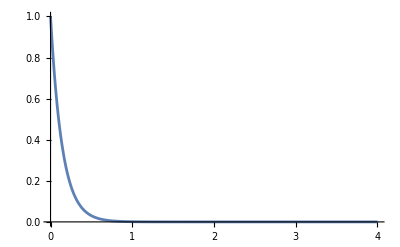

```mathematica
Plot[Exp[λ[[1]]t],{t,0,4},PlotRange->All]
```

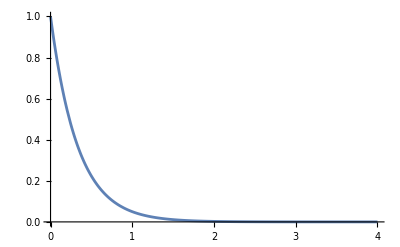

```mathematica
Plot[Exp[λ[[2]]t],{t,0,4},PlotRange->All]
```

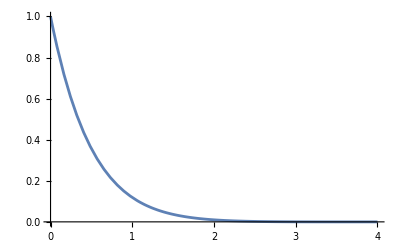

```mathematica
Plot[Exp[Re[λ[[3]]]t]Cos[Im[λ[[3]]]t],{t,0,4},PlotRange->All]
```

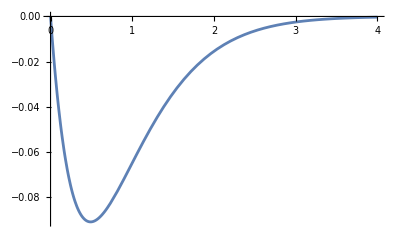

```mathematica
Plot[Exp[Re[λ[[4]]]t]Sin[Im[λ[[4]]]t],{t,0,4},PlotRange->All]
```

## Creo la matrice di cambiamento di base

```mathematica
T0=Transpose[Eigenvectors[A]]
```

{{151/294,11/18,2097/2890+(328 ⅈ)/1445,2097/2890-(328 ⅈ)/1445},{-24/49,-4/9,-229/578+(16 ⅈ)/289,-229/578-(16 ⅈ)/289},{172/147,14/9,2777/1445+(826 ⅈ)/1445,2777/1445-(826 ⅈ)/1445},{1,1,1,1}}

```mathematica
T=Transpose[{T0[[All,1]],T0[[All,2]],Re[T0[[All,3]]],Im[T0[[All,4]]]}]
```

{{151/294,11/18,2097/2890,-328/1445},{-24/49,-4/9,-229/578,-16/289},{172/147,14/9,2777/1445,-826/1445},{1,1,1,0}}

### Vediamo se la Forma Canonica è diagonale a blocchi, ci aspettiamo la presenza di un blocco di Jordan 2x2 data la presenza di autovalori complessi e coniugati

```mathematica
Λ=Simplify[Inverse[T].A.T]
```

{{-7,0,0,0},{0,-3,0,0},{0,0,-2,-1/2},{0,0,1/2,-2}}

```mathematica
Λ // MatrixForm
```

(-7 | 0 | 0 | 0
0 | -3 | 0 | 0
0 | 0 | -2 | -1/2
0 | 0 | 1/2 | -2)

## Calcolo della Risposta Libera

### Inizializzo il vettore delle condizioni iniziali

```mathematica
Subscript[x, 0]={{-1},{0},{-3},{0}};
```

### Proietto lo stato iniziale lungo le colonne della matrice “ibrida” T

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{2499/101},{-63},{3864/101},{2641/202}}

```mathematica
σ= Re[λ[[3]]]
```

-2

```mathematica
ω= Im[λ[[3]]]
```

1/2

### Calcolo la risposta libera sfruttando la decomposizione modale

```mathematica
(*Subscript[x, l][t_]:=FullSimplify[T.({{Exp[λ[[1]]t], 0, 0, 0}, {0, Exp[λ[[2]]t], 0, 0}, {0, 0, Exp[σ t]Cos[ω t], Exp[σ t]Sin[ω t]}, {0, 0, -Exp[σ t]Sin[ω t], Exp[σ t]Cos[ω t]}}).Subscript[z, 0]];*)
```

```mathematica
Subscript[x, l][t_]:=FullSimplify[T.MatrixExp[Λ t].Subscript[z, 0]]
```

```mathematica
Subscript[y, l][t_]:=C1.Subscript[x, l][t];
```

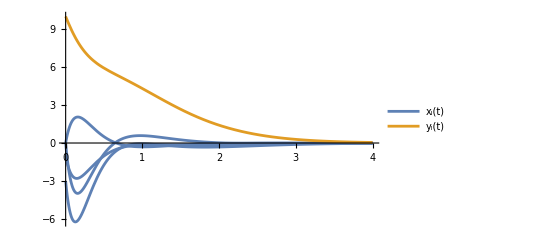

```mathematica
Plot[{Subscript[x, l][t],Subscript[y, l][t]},{t,0,4},PlotRange->All,PlotLegends->"Expressions"]
```

## Vediamo cosa accade quando cambiano le condizioni iniziali

```mathematica
T //MatrixForm
```

(151/294 | 11/18 | 2097/2890 | -328/1445
-24/49 | -4/9 | -229/578 | -16/289
172/147 | 14/9 | 2777/1445 | -826/1445
1 | 1 | 1 | 0)

Tramite l’analisi della combinazione lineare delle colonne associate agli autovalori reali, ottengo

```mathematica
Subscript[x, 0]= T[[All,1]]-6663/344+T[[All,2]] 6663/344
```

{2221/1176,11105/12642,188785/25284,0}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{-6663/344,6663/344,0,0}

```mathematica
Subscript[x, l][t_]:=Simplify[T.MatrixExp[Λ t].Subscript[z, 0]]
```

```mathematica
Subscript[x, l][t]
```

{(2221 ⅇ^(-7 t) (-453+539 ⅇ^(4 t)))/101136,-(2221 ⅇ^(-7 t) (-54+49 ⅇ^(4 t)))/12642,(2221 ⅇ^(-7 t) (-258+343 ⅇ^(4 t)))/25284,6663/344 ⅇ^(-7 t) (-1+ⅇ^(4 t))}

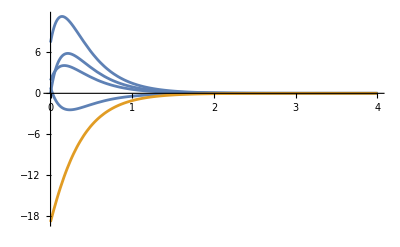

```mathematica
Plot[{Subscript[x, l][t],Subscript[y, l][t]},{t,0,4},PlotRange->All]
```

Tramite l’analisi della combinazione lineare delle colonne associate agli autovalori complessi e coniugati, ottengo

```mathematica
Subscript[x, 0]= T[[All,3]]1+T[[All,4]]1
```

{1441/2890,-261/578,1951/1445,1}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{0,0,1,1}

```mathematica
Subscript[x, l][t_]:=Simplify[T.MatrixExp[Λ t].Subscript[z, 0]]
```

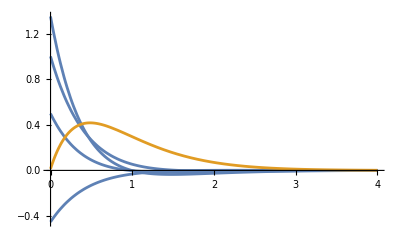

```mathematica
Plot[{Subscript[x, l][t],Subscript[y, l][t]},{t,0,4},PlotRange->All]
```

“Accendo” il primo modo naturale

{151/294,-24/49,172/147,1}

{1,0,0,0}

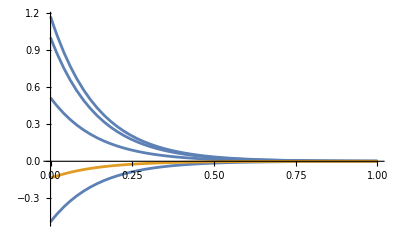

```mathematica
Subscript[x, 0]=Transpose[T][[1]]
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
Plot[{Subscript[x, l][t],Subscript[y, l][t]},{t,0,1},PlotRange->All]
```

“Accendo” il secondo modo naturale

{11/18,-4/9,14/9,1}

{0,1,0,0}

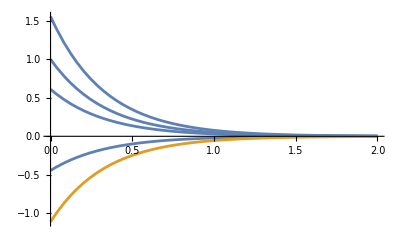

```mathematica
Subscript[x, 0]=Transpose[T][[2]]
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
Plot[{Subscript[x, l][t],Subscript[y, l][t]},{t,0,2},PlotRange->All]
```

“Accendo” il terzo modo naturale

{2097/2890,-229/578,2777/1445,1}

{0,0,1,0}

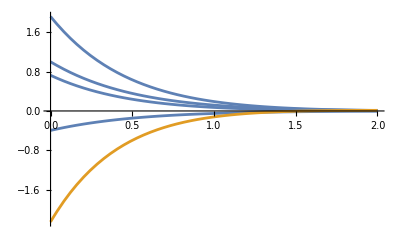

```mathematica
Subscript[x, 0]=Transpose[T][[3]]
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
Plot[{Subscript[x, l][t],Subscript[y, l][t]},{t,0,2},PlotRange->All]
```

“Accendo” il quarto modo naturale

{-328/1445,-16/289,-826/1445,0}

{0,0,0,1}

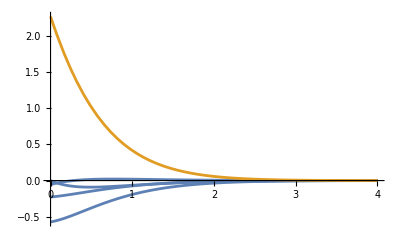

```mathematica
Subscript[x, 0]=Transpose[T][[4]]
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
Plot[{Subscript[x, l][t],Subscript[y, l][t]},{t,0,4},PlotRange->All]
```

## Calcolo della Funzione di Trasferimento

```mathematica
G[s_]:=Simplify[(C1.Inverse[s IdentityMatrix[4]-A].B)]
```

```mathematica
G[s]
```

{{(20 (-1+s))/(357+506 s+261 s^2+56 s^3+4 s^4)}}

normalizzo la funzione di trasferimento

```mathematica
FdT[s_]:= (Numerator[G[s]]/4)/(s^4+14 s^3+261/4 s^2+253/2 s+357/4)
```

```mathematica
FdT[s]
```

{{(5 (-1+s))/(357/4+(253 s)/2+(261 s^2)/4+14 s^3+s^4)}}

#### Per assicurarci che i calcoli siano corretti, possiamo determinare la FdT ed i suoi Poli e Zeri tramite delle funzioni offerte da Mathematica

```mathematica
Σ= StateSpaceModel[{A,B,C1}];
```

```mathematica
TransferFunctionModel[Σ]
```

(-5+5 s)/(357/4+(253 s)/2+(261 s^2)/4+14 s^3+s^4)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s11-53571FalseFalseFalseAutomaticNoneAutomatic

### Calcolo i Poli della Funzione di Trasferimento

```mathematica
Solve[Denominator[FdT[s][[1]]]==0,s]
```

{{s→-7},{s→-3},{s→-2-ⅈ/2},{s→-2+ⅈ/2}}

```mathematica
{{s->-7},{s->-3},{s->-2-ⅈ/2},{s->-2+ⅈ/2}}
TransferFunctionPoles[Σ]
```

{{s→-7},{s→-3},{s→-2-ⅈ/2},{s→-2+ⅈ/2}}

{{{-7,-3,-2-ⅈ/2,-2+ⅈ/2}}}

### Calcolo gli Zeri della Funzione di Trasferimento

```mathematica
Solve[Numerator[FdT[s][[1]]]==0,s]
TransferFunctionZeros[Σ]
```

{{s→1}}

{{{1}}}

## Risposta al Gradino Unitario

```mathematica
Factor[FdT[s]]
```

{{(20 (-1+s))/((3+s) (7+s) (17+16 s+4 s^2))}}

La risposta al Gradino unitario e’ pari a

```mathematica
U[s_]:=LaplaceTransform[UnitStep[t],t,s]
```

```mathematica
Y[s_]:= Factor[FdT[s] U[s]]
Y[s]
```

{{(20 (-1+s))/(s (3+s) (7+s) (17+16 s+4 s^2))}}

```mathematica
Apart[Y[s]]
```

{{-20/(357 s)+4/(3 (3+s))-40/(707 (7+s))-(16 (549+524 s))/(1717 (17+16 s+4 s^2))}}

Scrivo in maniera verbosa i fratti semplici

```mathematica
Subscript[C, 1]/s+Subscript[C, 1]/(s+3)+Subscript[C, 3]/(s+7)+Subscript[C, 4]/(s+2-ⅈ/2)+Subscript[C, 5]/(s+2+ⅈ/2)
```

C_1/s+C_1/(3+s)+C_3/(7+s)+C_4/((2-ⅈ/2)+s)+C_5/((2+ⅈ/2)+s)

Trovo il valore delle C, tramite la formula di Heaviside

```mathematica
Subscript[C, 1]=lim_(s->0) (s) Y[s][[1,1]]
```

-20/357

```mathematica
Subscript[C, 2]=lim_(s->-3) (s+3) Y[s][[1,1]]
```

4/3

```mathematica
Subscript[C, 3]=lim_(s->-7) (s+7) Y[s][[1,1]]
```

-40/707

```mathematica
Subscript[C, 4]=lim_(s->-2+ⅈ/2) (s+2-1/2 ⅈ) *Y[s][[1,1]]
```

-1048/1717-(1996 ⅈ)/1717

```mathematica
Subscript[C, 5]=Conjugate[Subscript[C, 4]]
```

-1048/1717+(1996 ⅈ)/1717

Scrivo ora la componente di regime della risposta forzata al segnale periodico elementare 1(t)

```mathematica
Subscript[y, f][t_]:=Subscript[C, 1] UnitStep[t]+Subscript[C, 2] Exp[-3 t] UnitStep[t]+Subscript[C, 3] Exp[-7 t] UnitStep[t]+2 Exp[-2 t]*ComplexExpand[Re[Subscript[C, 4] Exp[-ⅈ/2 t]]] UnitStep[t]
```

```mathematica
Subscript[y, ss][t_]:=Subscript[C, 1] UnitStep[t]
```

```mathematica
Subscript[y, tr][t_]:=Subscript[C, 2] Exp[-3 t] UnitStep[t]+Subscript[C, 3] Exp[-7 t] UnitStep[t]+2 Exp[-2 t]*ComplexExpand[Re[Subscript[C, 4] Exp[-ⅈ/2 t]]] UnitStep[t]
```

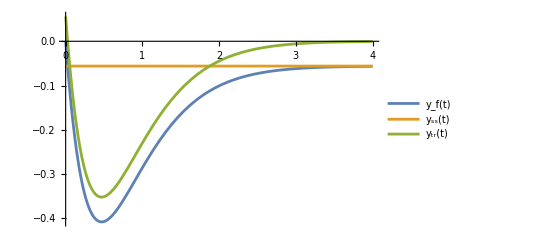

```mathematica
Plot[{Subscript[y, f][t],Subscript[y, ss][t],Subscript[y, tr][t]},{t,0,4},PlotRange->All,PlotLegends->"Expressions"]
```

## Forma Amplitude Phase

```mathematica
(*condisero lap di sin(1)1(t)*)
```

```mathematica
U[s_]:= LaplaceTransform[Sin[ t]UnitStep[t],t,s]
```

```mathematica
Y[s_]:= FdT[s][[1,1]]U[s]
```

```mathematica
Apart[Y[s]]
```

-2/(5 (3+s))+4/(505 (7+s))+(2 (7+11 s))/(425 (1+s^2))+(64 (493+913 s))/(42925 (17+16 s+4 s^2))

```mathematica
Subscript[D, 1]/(s+3)+Subscript[D, 2]/(s+7)+Subscript[D, 3]/(s+ⅈ)+Subscript[D, 4]/(s-ⅈ)+Subscript[D, 5]/(s+2-ⅈ/2)+Subscript[D, 6]/(s+2+ⅈ/2)
```

D_1/(3+s)+D_2/(7+s)+D_3/(ⅈ+s)+D_4/(-ⅈ+s)+D_5/((2-ⅈ/2)+s)+D_6/((2+ⅈ/2)+s)

```mathematica
Subscript[D, 1]=lim_(s->-3) (s+3) Y[s]
```

-2/5

```mathematica
Subscript[D, 2]=lim_(s->-7) (s+7)Y[s]
```

4/505

```mathematica
Subscript[D, 3]=lim_(s->-ⅈ) (s+ⅈ)Y[s]
```

11/425+(7 ⅈ)/425

```mathematica
Subscript[D, 4]=lim_(s->ⅈ) (s-ⅈ)Y[s]
```

11/425-(7 ⅈ)/425

```mathematica
Subscript[D, 5]=lim_(s->-2+ⅈ/2) (s+2-1/2 ⅈ) Y[s]
```

7304/42925+(21328 ⅈ)/42925

```mathematica
Subscript[D, 6]=Conjugate[Subscript[D, 5]]
```

7304/42925-(21328 ⅈ)/42925

```mathematica
Subscript[y, ss][t_]:= 2ComplexExpand[Re[Subscript[D, 4] Exp[I t]]]
```

```mathematica
Subscript[y, ss][t]
```

2 ((11 Cos[t])/425+(7 Sin[t])/425)

```mathematica
(* determino il fattore di distorsione, fra uscita a regime d'ingresso, dobbiamo scrivere la regime nella forma Ampiezza-fase, la pulsazione è identica nelle due formme, la distorsione non avviene sulla pulsazione*)
```

```mathematica
Solve[{(2 ((11Cos[t])/425+(7 Sin[t])/425)==X Sin[t+ψ])/.{t->0},(D[2 (+(11Cos[t])/425+(7 Sin[t])/425),t]==D[X Sin[ t+ψ],t])/.{t->0},X>0},{X,ψ}]
```

{{X→ConditionalExpression[(2 √(2/85))/5, C[1]∈ℤ],ψ→ConditionalExpression[-2 ArcTan[(-170+7 √170)/(11 √170)]+2 π C[1], C[1]∈ℤ]}}

```mathematica
(*il sistema ha un'ampiezza minore dell'unità, il segnale è attenuato, il sistema è in anticipo di psi*)
N[(2 √(2/85))/5]
```

0.0613572

```mathematica
N[-2 ArcTan[(-170+7 √170)/(11 √170)]](180/π)
```

57.5288

```mathematica
Subscript[y, trs][t_]:=Subscript[D, 1] Exp[-3 t]+Subscript[D, 2] Exp[-7 t]+2 Exp[-2 t]*ComplexExpand[Re[Subscript[D, 5] Exp[-ⅈ/2 t]]] UnitStep[t]
```

```mathematica
(* siccome la pulsazione non varia fra una forma e l'altra, il fattore di alterazione è dato da ampiezza e fase *)
```

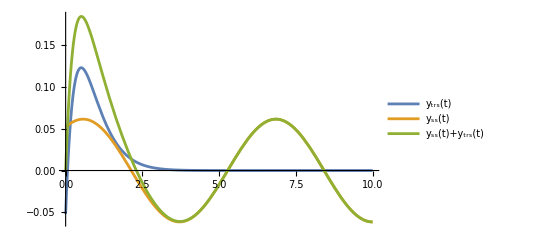

```mathematica
Plot[{Subscript[y, trs][t],Subscript[y, ss][t],Subscript[y, ss][t]+Subscript[y, trs][t]},{t,0,10},PlotRange->All,PlotLegends->"Expressions"]
```

```mathematica
X= 0.06135719910778964;
ω=1;
ψ=57.528807709151515;
```

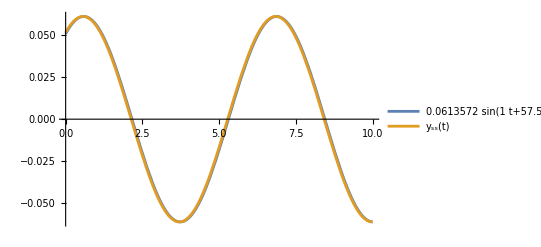

```mathematica
Plot[{X Sin[ω t+ ψ], Subscript[y, ss][t]},{t,0,10},PlotRange->All,PlotLegends->"Expressions"]
```

## Risposta al segnale periodico

```mathematica
X= 2;
ω=2;
ψ=0;
U[s_]:= LaplaceTransform[X Sin[ ω t + ψ] UnitStep[t],t,s]
Y[s_]:= FdT[s][[1]][[1]]U[s]
Y[s]
```

(20 (-1+s))/((4+s^2) (357/4+(253 s)/2+(261 s^2)/4+14 s^3+s^4))

```mathematica
Apart[Y[s]]
```

-16/(13 (3+s))+160/(5353 (7+s))-(16 (-1751+341 s))/(141245 (4+s^2))+(256 (413+401 s))/(20705 (17+16 s+4 s^2))

```mathematica
Subscript[Q, 1]/(s+3)+Subscript[Q, 2]/(s+7)+Subscript[Q, 3]/(s+2ⅈ)+Subscript[Q, 4]/(s-2ⅈ)+Subscript[Q, 5]/(s+2-ⅈ/2)+Subscript[Q, 6]/(s+2+ⅈ/2);
```

```mathematica
Subscript[Q, 1]=lim_(s->-3) (s+3) Y[s];
Subscript[Q, 2]=lim_(s->-7) (s+7)Y[s];
Subscript[Q, 3]=lim_(s->-2ⅈ) (s+2ⅈ)Y[s];
Subscript[Q, 4]=lim_(s->2ⅈ) (s-2ⅈ)Y[s];
Subscript[Q, 5]=lim_(s->-2+ⅈ/2) (s+2-1/2 ⅈ) Y[s];
Subscript[Q, 6]=Conjugate[Subscript[Q, 5]];
```

```mathematica
Subscript[y, ssin][t_]:= 2ComplexExpand[Re[Subscript[Q, 4] Exp[2*I t]]]
```

```mathematica
Subscript[y, trsin][t_]:=Subscript[Q, 1] Exp[-3 t]+Subscript[Q, 2] Exp[-7 t]+2 Exp[-2 t]*ComplexExpand[Re[Subscript[Q, 5] Exp[-ⅈ/2 t]]] UnitStep[t]
```

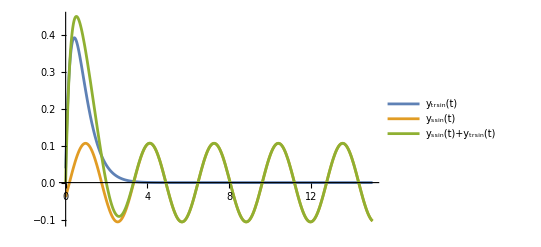

```mathematica
Plot[{Subscript[y, trsin][t],Subscript[y, ssin][t],Subscript[y, ssin][t]+Subscript[y, trsin][t]},{t,0,15},PlotRange->All,PlotLegends->"Expressions"]
```

## Modello Arma

## Ricavo il modello arma equivalente

```mathematica
Subscript[x, 0]={{-3},{2},{-3},{3}};
```

```mathematica
Ob={C1[[1]],C1[[1]].A,C1[[1]].A.A,C1[[1]].A.A.A}
```

{{-10,0,0,5},{0,10,5,0},{10,-10,-10,-5},{875/2,1655/2,-1005/4,2085/4}}

```mathematica
vettoreCondizioniIniziali= {{Subscript[y, 0]},{Subscript[y, 1]},{Subscript[y, 2]},{Subscript[y, 3]}}
```

{{y_0},{y_1},{y_2},{y_3}}

```mathematica
vettoreCondizioniIniziali= Ob.Subscript[x, 0]
```

{{45},{5},{-35},{2660}}

```mathematica
FdT[s][[1]][[1]]
```

(5 (-1+s))/(357/4+(253 s)/2+(261 s^2)/4+14 s^3+s^4)

```mathematica
modelloARMA= Expand[Denominator[FdT[s][[1]][[1]]]*Subscript[Y, ARMA][s]]== Expand[Numerator[FdT[s][[1]][[1]]]Subscript[U, ARMA][s]]
```

(357 Y_ARMA[s])/4+253/2 s Y_ARMA[s]+261/4 s^2 Y_ARMA[s]+14 s^3 Y_ARMA[s]+s^4 Y_ARMA[s]==-5 U_ARMA[s]+5 s U_ARMA[s]

```mathematica
(*Abbiamo una rappresentazione quivalente I/U, (modello ARMA). E' noto come "Equivalente", in quanto, per qualsiasi ingresso, la risposta forzata sarà così, ossia equivalente in ambo le rappresentazioni*)
```

```mathematica
InverseLaplaceTransform[(357 Subscript[Y, ARMA][s])/4+253/2 s Subscript[Y, ARMA][s]+261/4 s^2 Subscript[Y, ARMA][s]+14 s^3 Subscript[Y, ARMA][s]+s^4 Subscript[Y, ARMA][s]==-5 Subscript[U, ARMA][s]+5 s Subscript[U, ARMA][s],s,t]/.{Subscript[Y, ARMA][s]->LaplaceTransform[y[t],t,s], Subscript[U, ARMA][s]->LaplaceTransform[u[t],t,s]} /.
{y[0]->0, y'[0]->0, y''[0]->0, y'''[0]->0, u[0]->0}
```

(357 y[t])/4+(253 y'[t])/2+(261 y''[t])/4+14 y^(3)[t]+y^(4)[t]==-5 u[t]+5 u'[t]

```mathematica
EqDifferenziale= (357 y[t])/4+(253 y'[t])/2+(261 y''[t])/4+14 Derivative[3][y][t]+Derivative[4][y][t]==-5 u[t]+5 u'[t]
```

(357 y[t])/4+(253 y'[t])/2+(261 y''[t])/4+14 y^(3)[t]+y^(4)[t]==-5 u[t]+5 u'[t]

```mathematica
(* porto l'eqauzione del dominio di Laplace*)
```

```mathematica
eqDiffLap=Simplify[LaplaceTransform[EqDifferenziale,t, s]/.
{LaplaceTransform[y[t],t,s]->Subscript[Y, ARMA][s],LaplaceTransform[u[t],t,s]->Subscript[U, ARMA][s],u[0]->0}];
```

```mathematica
eqDiffLap
```

(357+506 s+261 s^2+56 s^3+4 s^4) Y_ARMA[s]==(506+261 s+56 s^2+4 s^3) y[0]+20 (-1+s) U_ARMA[s]+261 y'[0]+56 s y'[0]+4 s^2 y'[0]+56 y''[0]+4 s y''[0]+4 y^(3)[0]

```mathematica
Ydif[s_]:=Collect[Solve[eqDiffLap,Subscript[Y, ARMA][s]][[1,1]][[2]], Subscript[U, ARMA][s]]
```

```mathematica
Ydif[s]
```

((-20+20 s) U_ARMA[s])/(357+506 s+261 s^2+56 s^3+4 s^4)+(506 y[0]+261 s y[0]+56 s^2 y[0]+4 s^3 y[0]+261 y'[0]+56 s y'[0]+4 s^2 y'[0]+56 y''[0]+4 s y''[0]+4 y^(3)[0])/(357+506 s+261 s^2+56 s^3+4 s^4)

```mathematica
RispostaLiberaARMA= ((506 y[0]+261 s y[0]+56 s^2 y[0]+4 s^3 y[0]+261 y'[0]+
56 s y'[0]+4 s^2 y'[0]+56 y''[0]+4 s y''[0]+4 Derivative[3][y][0])/(357+506 s+261 s^2+56 s^3+4 s^4)) /. {y[0] ->vettoreCondizioniIniziali[[1,1]],y'[0]->vettoreCondizioniIniziali[[2,1]],
 y''[0]->vettoreCondizioniIniziali[[3,1]],Derivative[3][y][0]-> vettoreCondizioniIniziali[[4,1]]}
```

(32755+11885 s+2540 s^2+180 s^3)/(357+506 s+261 s^2+56 s^3+4 s^4)

```mathematica
(* per assicurarci che sia corretto, ottengo la risposta libera anche dalla definizione*)
```

```mathematica
RispostaLiberaConfronto =Simplify[C1.Inverse[s IdentityMatrix[4] - A].Subscript[x, 0]][[1,1]]
```

(5 (6551+2377 s+508 s^2+36 s^3))/(357+506 s+261 s^2+56 s^3+4 s^4)

## Risposta alla rampa unitaria

```mathematica
EqDifferenzialeRampa= (357 y[t])/4+(253 y'[t])/2+(261 y''[t])/4+14 Derivative[3][y][t]+Derivative[4][y][t]==-5 u[t]+5 u'[t]
```

(357 y[t])/4+(253 y'[t])/2+(261 y''[t])/4+14 y^(3)[t]+y^(4)[t]==-5 u[t]+5 u'[t]

```mathematica
(* Uso il modello ARMA per calcolare la risposta forzata*)
armaRampa=Simplify[LaplaceTransform[EqDifferenzialeRampa,t,s]/.{LaplaceTransform[y[t],t,s]->Subscript[Y, ARMA][s],LaplaceTransform[u[t],t,s]->Subscript[U, ARMA][s],u[0]->0}]
```

(357+506 s+261 s^2+56 s^3+4 s^4) Y_ARMA[s]==(506+261 s+56 s^2+4 s^3) y[0]+20 (-1+s) U_ARMA[s]+261 y'[0]+56 s y'[0]+4 s^2 y'[0]+56 y''[0]+4 s y''[0]+4 y^(3)[0]

```mathematica
Yarm[s]=Collect[Solve[armaRampa,Subscript[Y, ARMA][s]][[1,1]][[2]],Subscript[U, ARMA][s]]
```

((-20+20 s) U_ARMA[s])/(357+506 s+261 s^2+56 s^3+4 s^4)+(506 y[0]+261 s y[0]+56 s^2 y[0]+4 s^3 y[0]+261 y'[0]+56 s y'[0]+4 s^2 y'[0]+56 y''[0]+4 s y''[0]+4 y^(3)[0])/(357+506 s+261 s^2+56 s^3+4 s^4)

```mathematica
(*sostiuisoo Subscript[U, ARMA][s] con il valore della Trasformata di Laplace della rampa e i valori di y'[0] con quelli calcolati in precedenza*)
```

```mathematica
Subscript[y, RA][t_]:=FullSimplify[InverseLaplaceTransform[Yarm[s]/.{Subscript[U, ARMA][s]->LaplaceTransform[t UnitStep[t],t,s],y[0] ->vettoreCondizioniIniziali[[1,1]],y'[0]->vettoreCondizioniIniziali[[2,1]],
 y''[0]->vettoreCondizioniIniziali[[3,1]],Derivative[3][y][0]-> vettoreCondizioniIniziali[[4,1]]},s,t]]
```

```mathematica
Subscript[y, RA][t]
```

17260/127449-(150390 ⅇ^(-7 t))/4949+(6791 ⅇ^(-3 t))/9-(20 t)/357-(8 ⅇ^(-2 t) (2478522 Cos[t/2]-5089109 Sin[t/2]))/29189

```mathematica
(*Separo i valori della risposta di regime e della risposta transitoria*)
```

```mathematica
Subscript[y, rampaSS][t]=17260/127449-(20 t)/357
```

17260/127449-(20 t)/357

```mathematica
Subscript[y, rampaTR][t]=-(150390 ⅇ^(-7 t))/4949+(6791 ⅇ^(-3 t))/9-(8 ⅇ^(-2 t) (2478522 Cos[t/2]-5089109 Sin[t/2]))/29189
```

-(150390 ⅇ^(-7 t))/4949+(6791 ⅇ^(-3 t))/9-(8 ⅇ^(-2 t) (2478522 Cos[t/2]-5089109 Sin[t/2]))/29189

## Determinare lo stato iniziale x0

```mathematica
(* il blu è un asintoto boliquo*)
xIncognite= {{Subscript[x, 1]},{Subscript[x, 2]},{Subscript[x, 3]},{Subscript[x, 4]}}
```

{{x_1},{x_2},{x_3},{x_4}}

```mathematica
libera=Simplify[C1.Inverse[s IdentityMatrix[4]-A].xIncognite][[1]][[1]]
```

-((5 (2 (275+257 s+56 s^2+4 s^3) x_1-8 (134+13 s+s^2) x_2+52 x_3-48 s x_3-4 s^2 x_3-867 x_4-257 s x_4-56 s^2 x_4-4 s^3 x_4))/(357+506 s+261 s^2+56 s^3+4 s^4))

```mathematica
(*numeratore di 3° grado, che dipende dai coefficenti del vettore delle x incognite, il denominatore è il polinomio carateristico*)
forzata= Simplify[FdT[s]/s][[1]][[1]]
```

(20 (-1+s))/(s (357+506 s+261 s^2+56 s^3+4 s^4))

```mathematica
(* calcoliamo la risposta a regime *)
regime= (FdT[0]/s)[[1]][[1]]
```

-20/(357 s)

```mathematica
(* calcolo transitorio come forzata-regime, se il termine in s al deniminatore scompare, il processo sarà andato a buon fine*)
transitorio= Factor[forzata-regime]
```

(20 (863+261 s+56 s^2+4 s^3))/(357 (3+s) (7+s) (17+16 s+4 s^2))

```mathematica
(* sommo libera e transitoria, ne estraggo il denominatore, per verificare che sia identicamente nullo*)
Numerator[Simplify[Expand[libera+transitorio]]]
```

5 (3452+1044 s+224 s^2+16 s^3-714 (275+257 s+56 s^2+4 s^3) x_1+2856 (134+13 s+s^2) x_2-18564 x_3+17136 s x_3+1428 s^2 x_3+309519 x_4+91749 s x_4+19992 s^2 x_4+1428 s^3 x_4)

```mathematica
(* il polinomio è di 3° grado e ho 4 incognite (le x)*)
CoefficientList[Numerator[Simplify[Expand[libera+transitorio]]],s]
```

{17260-981750 x_1+1913520 x_2-92820 x_3+1547595 x_4,5220-917490 x_1+185640 x_2+85680 x_3+458745 x_4,1120-199920 x_1+14280 x_2+7140 x_3+99960 x_4,80-14280 x_1+7140 x_4}

```mathematica
(* eguaglio a 0 il sistema per trovare i cooefficenti*)
Solve[CoefficientList[Numerator[Simplify[Expand[libera+transitorio]]],s]=={0,0,0,0},{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4]}]
```

{{x_1→2/357,x_2→-2/357,x_3→4/357,x_4→0}}

```mathematica
response= FullSimplify[OutputResponse[{Σ,{2/357,-2/357,4/357,0}},1,t]]
```

{-20/357}

```mathematica
FdT[0]
```

{{-20/357}}

## Calcolo della risposta per un sistema LTI-TC all’ingresso 1(-t)

```mathematica
(*1. Valutazione della risposta per t<0.*)
yNeg= FdT[0][[1]][[1]]
```

-20/357

```mathematica
(*2. Valutazione della risposta per t>0.*)
```

```mathematica
Subscript[x, 0]=Inverse[Ob].{{FdT[0][[1]][[1]]},{0},{0},{0}}
```

{{949/105672},{-2/357},{4/357},{1/148}}

```mathematica
yliberas=Simplify[(C1.Inverse[s IdentityMatrix[4]-A].Subscript[x, 0])[[1]][[1]]]
```

-(20 (506+261 s+56 s^2+4 s^3))/(357 (357+506 s+261 s^2+56 s^3+4 s^4))

```mathematica
Apart[yliberas]
```

-1/(3 (3+s))+5/(707 (7+s))+(64 (14+29 s))/(1717 (17+16 s+4 s^2))

```mathematica
Subscript[H, 1]=lim_(s->-3) (s+3) yliberas
```

-1/3

```mathematica
Subscript[H, 2]=lim_(s->-7) (s+7)yliberas
```

5/707

```mathematica
Subscript[H, 3]=lim_(s->-2+ⅈ/2) ((2-ⅈ/2)+s)yliberas
```

232/1717+(704 ⅈ)/1717

```mathematica
Subscript[H, 4]= Conjugate[Subscript[H, 3]]
```

232/1717-(704 ⅈ)/1717

```mathematica
yliberat=Subscript[H, 1] Exp[-3 t]+Subscript[H, 2] Exp[-7 t]+2 Exp[-2 t]*ComplexExpand[Re[Subscript[H, 4] Exp[-ⅈ/2 t]]] UnitStep[t]
```

(5 ⅇ^(-7 t))/707-ⅇ^(-3 t)/3+2 ⅇ^(-2 t) ((232 Cos[t/2])/1717-(704 Sin[t/2])/1717) UnitStep[t]

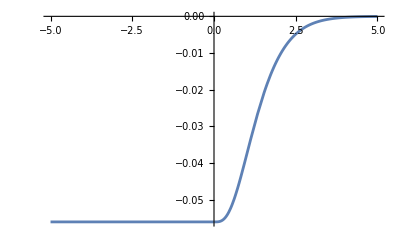

```mathematica
y[t_]:=Piecewise[{{yNeg, t<0}, {yliberat, t>=0}}]
Plot[y[t],{t,-5,5},PlotRange->All]
```